## Скрытая марковская модель

### Рассмотрим двоих друзей, Алису и Боба, которые живут далеко друг от друга и каждый день говорят по телефону о том, что они делали в тот день. Боб заинтересован только в трех мероприятиях : - прогулки в парке, - посещения магазинов - уборки квартиры. Выбор того, что нужно сделать, это определяется исключительно погодой на данный день. Алиса не имеет определенной информации о погоде в городе, где живет Боб, но она знает, что общие тенденции. Основываясь на том, что Боб говорит ей, что он делал каждый день, Алиса пытается угадать, какая погода должна быть у него. Алиса знает среднее состояние погоды в этом районе, а также то, что Боб любит делать. Состояние погоды: 1 - Дождь 2 - Солнечно Состояние Боба: 1 - Прогулка 2 - Магазин 3 - Уборка

-Graphics-

0.571429

0.428571

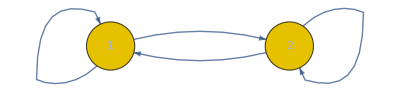

```mathematica
Clear["Global`*"]
States={0.6,0.4};
TransitionMatrix={{0.7,0.3},{0.4,0.6}};
EmissionMatrix={{0.1,0.4,0.5},{0.6,0.3,0.1}};

dmp=DiscreteMarkovProcess[States,TransitionMatrix];
PDF[StationaryDistribution[dmp],1]
PDF[StationaryDistribution[dmp],2]
Graph[dmp]
```

```mathematica
hmm=HiddenMarkovProcess[States,TransitionMatrix,EmissionMatrix]; (*символьное моделирование*)
PDF[StationaryDistribution[hmm],1](*вероятность прогулки*)
PDF[StationaryDistribution[hmm],2](*вероятность шопинга*)
PDF[StationaryDistribution[hmm],3](*вероятность уборки*)
```

0.314286

0.357143

0.328571

```mathematica
data=RandomFunction[hmm,{1,100000}]; (*численное моделирование*)
Count[data["Values"],1]/100000.(*вероятность прогулки*)
Count[data["Values"],2]/100000.(*вероятность шопинга*)
Count[data["Values"],3]/100000.(*вероятность уборки*)
```

0.31334

0.35736

0.3293

#### Какое наиболее вероятное состояние погоды , если Боб три дня подряд убирает квартиру?

```mathematica
fhmm=FindHiddenMarkovStates[{3,3,3},hmm]
```

{1,1,1}

#### Какое наиболее вероятное состояние погоды , если Боб:

```mathematica
fhmm=FindHiddenMarkovStates[{1,2,3},hmm](*прогулка, шопинг, уборка*)
```

{2,1,1}

```mathematica
fhmm=FindHiddenMarkovStates[{3,1,2},hmm] (*уборка, прогулка, шопинг*)
```

{1,2,2}

```mathematica
fhmm=FindHiddenMarkovStates[{3,2,1},hmm](*уборка, шопинг, прогулка*)
```

{1,1,2}

### Рассмотрим деревню, где все жители деревни либо: 1 - здоровы 2 - больны и только сельский врач может определить, болен ли житель. Врач ставит диагноз, спрашивая пациентов, как они чувствуют. Сельские жители могут только ответить , что они чувствуют себя: 1 - нормально, 2 - у них озноб 3 - у них головокружение . Врач считает, что состояние здоровья его пациентов работает на основе дискретной марковской цепи. Есть два состояние “Здоровый“ и “Больной“, но врач не может наблюдать их непосредственно, они скрыты от него (врач ориентируется на результаты опроса пациента для вынесения диагноза). Ежедневно существует определенная вероятность того, что пациент будет сообщит врачу, что его самочувствие является: нормальным, есть озноб, или есть головокружение, в зависимости состояния здоровья.

-Graphics-

```mathematica
Clear["Global`*"]
States={0.6,0.4};
TransitionMatrix={{0.7,0.3},{0.4,0.6}};
EmissionMatrix={{0.5,0.4,0.1},{0.1,0.3,0.6}};
dmm=DiscreteMarkovProcess[States,TransitionMatrix];
hmm=HiddenMarkovProcess[States,TransitionMatrix,EmissionMatrix];
fhmm=FindHiddenMarkovStates[{1,2,3},hmm]
```

{1,1,2}

```mathematica
path={1,2,3};
FindHiddenMarkovStates[path,hmm,"ViterbiDecoding"](*по умолчанию максимизирует вероятность скрытой последовательности*)
FindHiddenMarkovStates[path,hmm,"PosteriorDecoding"](*максимизирует вероятность скрытого состояния в каждый момент времени*)
```

{1,1,2}

{1,1,2}

```mathematica
path={2,3,2};
FindHiddenMarkovStates[path,hmm,"ViterbiDecoding"]
FindHiddenMarkovStates[path,hmm,"PosteriorDecoding"]
```

{1,2,2}

{1,2,1}

```mathematica
Likelihood[hmm,{1,2,3}](*вероятность получения последовательности наблюдений*)
Probability[x[0]==1&&x[1]==2&&x[2]==3,x\[Distributed]hmm]
```

0.03628

0.03628

#### Алгоритм Витерби (по умолчанию), найдем совместную вероятность скрытых состояний марковской цепи и наблюдений

```mathematica
Clear["Global`*"]
States={0.6,0.4};
TransitionMatrix={{0.7,0.3},{0.4,0.6}};
EmissionMatrix={{0.5,0.4,0.1},{0.1,0.3,0.6}};
hmm=HiddenMarkovProcess[States,TransitionMatrix,EmissionMatrix];

(* hmm - дискретный скрытый марковский процесс *)
(* states - вектор состояние марковской цепи *)
(* emissions - вектор наблюдений (выбросов) *)
(* результат совместная вероятность скрытых состояний марковской цепи и наблюдений (выбросов)*)

jointLikelihood[hmm_?ProcessParameterQ,states_?VectorQ,emissions_?VectorQ]:=Likelihood[DiscreteMarkovProcess[hmm],states]*Times@@MapThread[Part[hmm[[3]],#1,#2]&,{states,emissions}]

jointLikelihood[hmm,{1,1,2},{1,2,3}]
jointLikelihood[hmm,{1,1,1},{1,2,3}]
```

0.01512

0.00588

#### Совместная вероятность скрытых состояний марковской цепи и наблюдений (выбросов) для одинаковых наблюдений но разных алгоритмов

```mathematica
emissions={2,3,2};
FindHiddenMarkovStates[emissions,hmm,"ViterbiDecoding"]
jointLikelihood[hmm,%,emissions]

FindHiddenMarkovStates[emissions,hmm,"PosteriorDecoding"]
jointLikelihood[hmm,%,emissions]
```

{1,2,2}

0.007776

{1,2,1}

0.006912

#### Алгоритм Витерби и Likelihood дают различный результат для скрытой марковской цепи

```mathematica
FindHiddenMarkovStates[{1,2,3},hmm](*поиск наиболее вероятных состояний марковской цепи при заданной наблюдаемом векторе*)
Likelihood[hmm,{1,2,3}](* вероятность получения последовательности наблюдений *)
jointLikelihood[hmm,{1,1,2},{1,2,3}](*совместная вероятность скрытых состояний марковской цепи и наблюдений (выбросов)*)
```

{1,1,2}

0.03628

0.01512

#### Внимание! FindHiddenMarkovStates дает только одно решение (возможно из нескольких)

```mathematica
statepaths=Tuples[{1,2},3]
loglikes=Table[jointLikelihood[hmm,stseq,emissions],{stseq,statepaths}]
Position[loglikes,Max[loglikes]]
```

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}

{0.004704,0.001512,0.006912,0.007776,0.001344,0.000432,0.006912,0.007776}

{{4},{8}}

### Модель рынка

```mathematica
Clear["Global`*"]
m={{0.95,0.05},{0.1,0.9}};
em={{0.6,0.3,0.1},{0.1,0.8,0.1}};
trade=Characters["uduududuedudduddeeddduudeududdeuuueeuu"]/.{"u"->1,"d"->2,"e"->3};
hmm=HiddenMarkovProcess[{0.5,0.5},m,em];
StringJoin[FindHiddenMarkovStates[trade,hmm]/.{1-> "G",2-> "B"}]
StringJoin[FindHiddenMarkovStates[trade,hmm,"PosteriorDecoding"]/.{1-> "G",2-> "B"}]
```

GGGGGGGGGGGGGGGGGGGGGGGGGGGGGGGGGGGGGG

GGGGGGGGGGGGGGBBBBBBBGGGGGGGGGGGGGGGGG

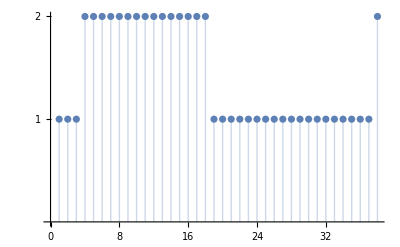

GGGBBBBBBBBBBBBBBBGGGGGGGGGGGGGGGGGGGB

{{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2}}

```mathematica
dmp=DiscreteMarkovProcess[{1,0},m];
data=RandomFunction[dmp,{1,Length[trade]}];
ListPlot[data,Filling->Axis,Ticks->{Automatic,{1,2}}]
StringJoin[data["ValueList"]/.{1-> "G",2-> "B"}]
```

### Модель c пропущенными данными

```mathematica
𝒫=HiddenMarkovProcess[{1/2,1/2},{{0.7,0.3},{0.2,0.8}},{{1/6,1/6,1/6,1/6,1/6,1/6},{1/10,1/10,1/10,1/10,1/10,1/2}}];
data={6,6,6,3,Missing[],Missing[],5,1,Missing[],5,4};
FindHiddenMarkovStates[data,𝒫]
```

{2,2,2,1,1,1,1,1,1,1,1}

### Найти наиболее вероятный переход

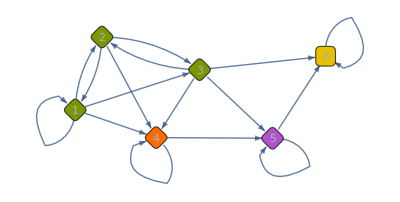

{1,6}

{1,4,5,6}

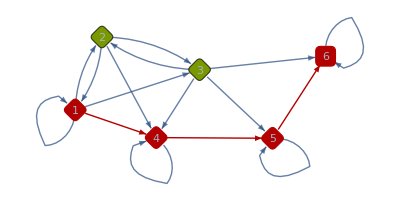

1/16

```mathematica
Clear["Global`*"]
m={{1/4,1/4,1/4,1/4,0,0},
{1/3,0,1/3,1/3,0,0},
{0,1/2,0,1/4,1/16,3/16},
{0,0,0,1/2,1/2,0},
{0,0,0,0,1/2,1/2},
{0,0,0,0,0,1}};
proc=DiscreteMarkovProcess[1,m];
g=Graph[proc]
hmm=HiddenMarkovProcess[1,m,{{1,0,0,0,0,0},None,None,None,None,{0,0,0,0,0,1}}];
obs={1,6}
path=FindHiddenMarkovStates[obs,hmm]
HighlightGraph[g,PathGraph[path,DirectedEdges->True]]

pathProbability[m_?MatrixQ,path_List]:=Times@@(m[[##]]&@@@Partition[path,2,1])
pathProbability[m,path]
```

-Graphics-

{1,5}

{1,4,5}

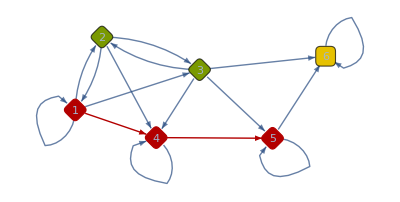

1/8

```mathematica
Clear["Global`*"]
m={{1/4,1/4,1/4,1/4,0,0},
{1/3,0,1/3,1/3,0,0},
{0,1/2,0,1/4,1/16,3/16},
{0,0,0,1/2,1/2,0},
{0,0,0,0,1/2,1/2},
{0,0,0,0,0,1}};
proc=DiscreteMarkovProcess[1,m];
g=Graph[proc]
hmm=HiddenMarkovProcess[1,m,({{1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}})];
obs={1,5}
path=FindHiddenMarkovStates[obs,hmm]
HighlightGraph[g,PathGraph[path,DirectedEdges->True]]

pathProbability[m_?MatrixQ,path_List]:=Times@@(m[[##]]&@@@Partition[path,2,1])
pathProbability[m,path]
```